# Brute-force classify

MSTに対して、CVI評価と最長エッジの削除を繰り返し、クラスタ数が1からNまでのCVIを得て、最良のCVIを持つクラシフィケーションを選択する。

必要なデータ: 
- 距離行列 (V * V)
- MST (2 * E)
- 連結行列(ノード同士が何ステップでつながっているか) (V * V)
- クラス分けリスト (V * V)

CVI:
CNS3 (mstPi2rkS[3] @ Cluster+Distance_Operations.txt)
CNS4 (mstPi2rkS[4] @ Cluster+Distance_Operations.txt)
Example - /Users/kouamano/gitsrc/ClusteringAdequation/ClusterValidityIndices_Sriparna_Exam(calc-index).nb

## 準備

```mathematica
$CharacterEncoding="UTF-8"
```

UTF-8

```mathematica
(*Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]*)
```

```mathematica
(*Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]*)
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]
```

```mathematica
(*SetDirectory["/Users/kouamano/gitsrc/Brute-force-classify"]*)
```

```mathematica
(*SetDirectory["/Users/amanokou/gitsrc/Brute-force-classify"]*)
```

```mathematica
SetDirectory["/home/kamano/gitsrc/Brute-force-classify"]
```

/home/kamano/gitsrc/Brute-force-classify

```mathematica
"/home/kamano/gitsrc/Brute-force-classify"
```

/home/kamano/gitsrc/Brute-force-classify

## Program

最初に最大長のエッジを得る:

```mathematica
getMaxEdge[mst]:=mst[[Ordering[mst,1,(#1[[3]]>#2[[3]])&]]][[1]][[{1,2}]]
```

最初に選んだエッジから最初のグループを作る:

```mathematica
makeFirstGr[edge_List,len_]:=Table[edge[[1]],{len}]
```

グループIDの判定、ステップが近い方のグループに書き換える:

```mathematica
getGroupBySortedEdge[sedge_,pos_,conj_,prev_]:=Module[{edge,li,len,target,disc},
edge=sedge[[pos]][[{1,2}]];
li= Transpose[conj[[edge]]];
len=Length[prev];
target=Union[prev[[edge]]];
disc=Map[If[#[[1]]<=#[[2]],edge[[1]],edge[[2]]]&,li];
Table[If[prev[[n]]==target[[1]],disc[[n]],prev[[n]]],{n,len}]
]
```

グループIDからクラスターを生成:

```mathematica
makeClusterByGr[li_]:=Module[{classes},
classes=Union[li];
Map[Flatten[Position[li,#]]&,classes]
]
```

一つのクラスターから一つのエッジグループを作成(3つの条件ごとにプログラム作成):

```mathematica
extractEdgeGrFromCl[mst_,cl_/;Length[cl]≤1]:={}
```

```mathematica
extractEdgeGrFromCl[mst_,cl_/;Length[cl]==2]:=Module[{mstEd},
mstEd=Map[Sort[{#[[1]],#[[2]]}]&,mst];
mst[[Flatten[Position[mstEd,Sort[cl]]]]]
]
```

```mathematica
extractEdgeGrFromCl[mst_,cl_/;Length[cl]≥3]:=Module[{mstEd,startEd,endEd,startContPos,endContPos},
mstEd=Map[Sort[{#[[1]],#[[2]]}]&,mst];
startEd=Map[#[[1]]&,mst];
endEd=Map[#[[2]]&,mst];
startContPos=Position[Map[ContainsAny[cl,{#}]&,startEd],True];
endContPos=Position[Map[ContainsAny[cl,{#}]&,endEd],True];
mst[[Flatten[Intersection[startContPos,endContPos]]]]
]
```

クラスターをエッジグループに変換:

```mathematica
makeEdgeGrFromCluster[mst_,cl_]:=Map[extractEdgeGrFromCl[mst,#]&,cl]
```

## Example

## 初期設定

データ:

```mathematica
data1={{0.7598461064538076,0.2762446676639849},{0.052506257778350385,0.4754933397861183},{0.835725205441473,0.971833104200341},{0.6256858201023905,0.39269853076870276},{0.8735494574667926,0.12663983198252038},{0.7508780147998599,0.6241170701623782},{0.2698064552281392,0.7247970742521272}}
```

{{0.759846,0.276245},{0.0525063,0.475493},{0.835725,0.971833},{0.625686,0.392699},{0.873549,0.12664},{0.750878,0.624117},{0.269806,0.724797}}

```mathematica
(*data1=Table[{RandomReal[],RandomReal[]},{7}]*)
```

距離行列:

```mathematica
(data1dmat=Outer[EuclideanDistance,data1,data1,1])//MatrixForm
```

(0. | 0.734867 | 0.699715 | 0.177653 | 0.18791 | 0.347988 | 0.664333
0.734867 | 0. | 0.927246 | 0.579128 | 0.892082 | 0.714011 | 0.330714
0.699715 | 0.927246 | 0. | 0.616047 | 0.846039 | 0.357918 | 0.617488
0.177653 | 0.579128 | 0.616047 | 0. | 0.363626 | 0.263111 | 0.486764
0.18791 | 0.892082 | 0.846039 | 0.363626 | 0. | 0.512379 | 0.849881
0.347988 | 0.714011 | 0.357918 | 0.263111 | 0.512379 | 0. | 0.491494
0.664333 | 0.330714 | 0.617488 | 0.486764 | 0.849881 | 0.491494 | 0.)

距離行列書き出し:

```mathematica
Export["data1.dmat",data1dmat,"TSV"]
```

data1.dmat

MST:

```mathematica
Run["/usr/local/bin/MST dmat=data1.dmat > data1.mst"]
```

0

MSTの読み込み:

```mathematica
(mst=Map[#+{1,1,0}&,Import["data1.mst","TSV"]])//TableForm
```

1 | 4 | 0.177653
1 | 5 | 0.18791
4 | 6 | 0.263111
6 | 3 | 0.357918
4 | 7 | 0.486764
7 | 2 | 0.330714

結合行列:

```mathematica
conjMat=conjMatFromAdjE[mst]
```

{{0,3,3,1,1,2,2},{3,0,4,2,4,3,1},{3,4,0,2,4,1,3},{1,2,2,0,2,1,1},{1,4,4,2,0,3,3},{2,3,1,1,3,0,2},{2,1,3,1,3,2,0}}

Plot:

:edge:

```mathematica
pos=Map[#[[{1,2}]]&,mst]
```

{{1,4},{1,5},{4,6},{6,3},{4,7},{7,2}}

:line coordinate:

```mathematica
cod=Map[data1[[#]]&,pos,{2}]
```

{{{0.759846,0.276245},{0.625686,0.392699}},{{0.759846,0.276245},{0.873549,0.12664}},{{0.625686,0.392699},{0.750878,0.624117}},{{0.750878,0.624117},{0.835725,0.971833}},{{0.625686,0.392699},{0.269806,0.724797}},{{0.269806,0.724797},{0.0525063,0.475493}}}

```mathematica
line=Map[Line[#]&,cod,{1}]
```

{Line[{{0.759846,0.276245},{0.625686,0.392699}}],Line[{{0.759846,0.276245},{0.873549,0.12664}}],Line[{{0.625686,0.392699},{0.750878,0.624117}}],Line[{{0.750878,0.624117},{0.835725,0.971833}}],Line[{{0.625686,0.392699},{0.269806,0.724797}}],Line[{{0.269806,0.724797},{0.0525063,0.475493}}]}

:Plot:

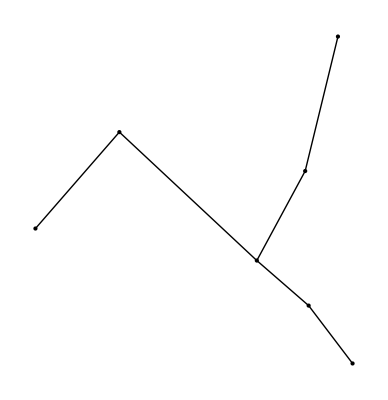

```mathematica
Graphics[{Map[Point,data1],line}]
```

## 手順

### 距離行列

```mathematica
data1dmat
```

{{0.,0.734867,0.699715,0.177653,0.18791,0.347988,0.664333},{0.734867,0.,0.927246,0.579128,0.892082,0.714011,0.330714},{0.699715,0.927246,0.,0.616047,0.846039,0.357918,0.617488},{0.177653,0.579128,0.616047,0.,0.363626,0.263111,0.486764},{0.18791,0.892082,0.846039,0.363626,0.,0.512379,0.849881},{0.347988,0.714011,0.357918,0.263111,0.512379,0.,0.491494},{0.664333,0.330714,0.617488,0.486764,0.849881,0.491494,0.}}

### MST

```mathematica
mst
```

{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111},{6,3,0.357918},{4,7,0.486764},{7,2,0.330714}}

### 結合行列

```mathematica
conjMat
```

{{0,3,3,1,1,2,2},{3,0,4,2,4,3,1},{3,4,0,2,4,1,3},{1,2,2,0,2,1,1},{1,4,4,2,0,3,3},{2,3,1,1,3,0,2},{2,1,3,1,3,2,0}}

### 各 k におけるクラスターの作成(experimental)

エッジリストをソート:

```mathematica
(sedge=Sort[mst,(#1[[3]]>#2[[3]])&])//TableForm
```

4 | 7 | 0.486764
6 | 3 | 0.357918
7 | 2 | 0.330714
4 | 6 | 0.263111
1 | 5 | 0.18791
1 | 4 | 0.177653

最初のグループ(1 class)を作成:

```mathematica
g[1]=makeFirstGr[sedge[[1]],Length[conjMat]]
```

{4,4,4,4,4,4,4}

:グループIDの判定、ステップが近い方のグループに書き換える:

```mathematica
g[2]=getGroupBySortedEdge[sedge,1,conjMat,g[1]]
```

{4,7,4,4,4,4,7}

:グループIDからクラスターを生成:

```mathematica
c[2]=makeClusterByGr[g[2]]
```

{{1,3,4,5,6},{2,7}}

:クラスターをエッジグループに変換:

```mathematica
makeEdgeGrFromCluster[mst,c[2]]
```

{{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111},{6,3,0.357918}},{{7,2,0.330714}}}

```mathematica
g[3]=getGroupBySortedEdge[sedge,2,conjMat,g[2]]
```

{6,7,3,6,6,6,7}

```mathematica
c[3]=makeClusterByGr[g[3]]
```

{{3},{1,4,5,6},{2,7}}

```mathematica
makeEdgeGrFromCluster[mst,c[3]]
```

{{},{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111}},{{7,2,0.330714}}}

```mathematica
makeClusterByGr[g[3]]
```

{{3},{1,4,5,6},{2,7}}

```mathematica
g[4]=getGroupBySortedEdge[sedge,3,conjMat,g[3]]
```

{6,2,3,6,6,6,7}

```mathematica
g[5]=getGroupBySortedEdge[sedge,4,conjMat,g[4]]
```

{4,2,3,4,4,6,7}

```mathematica
g[6]=getGroupBySortedEdge[sedge,5,conjMat,g[5]]
```

{1,2,3,1,5,6,7}

```mathematica
g[7]=getGroupBySortedEdge[sedge,6,conjMat,g[6]]
```

{1,2,3,4,5,6,7}

### 各 k におけるクラスター、エッジグループの作成(Table)

k=2 :: N-1 までグループIDを生成

```mathematica
idList=Table[g[n+1]=getGroupBySortedEdge[sedge,n,conjMat,g[n]],{n,Length[conjMat]-2}]
```

{{4,7,4,4,4,4,7},{6,7,3,6,6,6,7},{6,2,3,6,6,6,7},{4,2,3,4,4,6,7},{1,2,3,1,5,6,7}}

k=2 :: N-1 までグループIDよりクラスターを生成

```mathematica
clusters=Map[makeClusterByGr,idList]
```

{{{1,3,4,5,6},{2,7}},{{3},{1,4,5,6},{2,7}},{{2},{3},{1,4,5,6},{7}},{{2},{3},{1,4,5},{6},{7}},{{1,4},{2},{3},{5},{6},{7}}}

クラスターよりエッジグループを生成

```mathematica
edgeGrs=Map[makeEdgeGrFromCluster[mst,#]&,clusters]
```

{{{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111},{6,3,0.357918}},{{7,2,0.330714}}},{{},{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111}},{{7,2,0.330714}}},{{},{},{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111}},{}},{{},{},{{1,4,0.177653},{1,5,0.18791}},{},{}},{{{1,4,0.177653}},{},{},{},{},{}}}

### CVIによる各クラスターの評価

クラスターごとのMST、リスト分けされたサンプルID、クラスごとの半径、全サンプル半径、が必要

プログラム:
/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt

```mathematica
(*Get["/Users/kouamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]*)
```

```mathematica
(*Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]*)
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]
```

全サンプル半径:

```mathematica
totalR=radiusOfAllClSamples[data1]
```

0.247464

各半径(サンプルIDのリストより):

```mathematica
eachR=Table[takeVecByID[data1,clusters[[n]]]//distancesFromEachClToCenter,{n,Length[clusters]}]
```

{{0.177162,0.442906},{0.517844,0.22292,0.442906},{0.544224,0.517844,0.22292,0.388378},{0.544224,0.517844,0.293774,0.191012,0.388378},{0.203443,0.544224,0.517844,0.476148,0.191012,0.388378}}

CVI評価:

:mstPi2rkS[3]:

```mathematica
Table[mstPi2rkS[3][edgeGrs[[n]]/.{}->{{0,0,0}},clusters[[n]],totalR],{n,Length[clusters]}]
```

{10.1778,6.67724,5.78218,5.90785,6.51882}

:mstPi2rkS[4]:

```mathematica
Table[mstPi2rkS[3][edgeGrs[[n]]/.{}->{{0,0,0}},clusters[[n]],eachR[[n]]],{n,Length[clusters]}]
```

{13.1667,6.15058,6.0216,5.7545,6.63686}

```mathematica
??mstPi2rkS
```

Global`mstPi2rkS

mstPi2rkS[1][mst_List,mstm_,cls_]:=Module[{k,numMems,mstmaxs,MSTmmax,MSTmmean},k=Length[cls];numMems=(Length[#1]&)/@cls;mstmaxs=(Max[#1]&)/@Map[#1⟦-1⟧&,mst,{2}];MSTmmax=Max[(#1⟦-1⟧&)/@mstm];MSTmmean=Mean[(#1⟦-1⟧&)/@mstm];k Inner[Power,numMems,mstmaxs/MSTmmean,Times]^(1/k)]
 
mstPi2rkS[2][mst_List,mstm_,cls_]:=Module[{k,numMems,mstmaxs,mstmeans,MSTmmax,mstmaxsS},k=Length[cls];numMems=(Length[#1]&)/@cls;mstmaxs=(Max[#1]&)/@Map[#1⟦-1⟧&,mst,{2}];mstmeans=(Mean[#1]&)/@Map[#1⟦-1⟧&,mst,{2}];MSTmmax=Max[(#1⟦-1⟧&)/@mstm];mstmaxsS=Table[(If[#1==0,0,#1/#2]&)[mstmaxs⟦i⟧,mstmeans⟦i⟧],{i,Length[mstmaxs]}];k Inner[Power,numMems,mstmaxsS,Times]^(1/k)]
 
mstPi2rkS[3][mst_List,mstm_,cls_,totalR_]:=Module[{k,numMems,mstmaxs,MSTmmax},k=Length[cls];numMems=(Length[#1]&)/@cls;mstmaxs=(Max[#1]&)/@Map[#1⟦-1⟧&,mst,{2}];k Inner[Power,numMems,mstmaxs/totalR,Times]^(1/k)]
 
mstPi2rkS[3][mst_List,cls_,totalR_]:=Module[{k,numMems,mstmaxs,MSTmmax},k=Length[cls];numMems=(Length[#1]&)/@cls;mstmaxs=(Max[#1]&)/@Map[#1⟦-1⟧&,mst,{2}];k Inner[Power,numMems,mstmaxs/totalR,Times]^(1/k)]
 
mstPi2rkS[4][mst_List,mstm_,cls_,clRs_]:=Module[{k,numMems,mstmaxs,MSTmmax},k=Length[cls];numMems=(Length[#1]&)/@cls;mstmaxs=(Max[#1]&)/@Map[#1⟦-1⟧&,mst,{2}];k Inner[Power,numMems,mstmaxs/clRs,Times]^(1/k)]
 
mstPi2rkS[4][mst_List,cls_,clRs_]:=Module[{k,numMems,mstmaxs,MSTmmax},k=Length[cls];numMems=(Length[#1]&)/@cls;mstmaxs=(Max[#1]&)/@Map[#1⟦-1⟧&,mst,{2}];k Inner[Power,numMems,mstmaxs/clRs,Times]^(1/k)]

## メモ

```mathematica
mstPi2rkS[3][edgeGrs[[4]]/.{}->{{0,0,0}},clusters[[4]],1]
```

5.21076